# Spatial ARGs

```mathematica
ClearAll
```

ClearAll

#### Figure 2 for Manuscript

```mathematica
Clear["Global`*"]
Ones[n_] := ConstantArray[1,{n,1}];
Zeros[n_] := ConstantArray[0,{n,1}];

S1 = {{t,t1,0},{t1,t,0},{0,0,t}} + te ConstantArray[1,{3,3}];
S2 = {{t,0,0},{0,t,t2},{0,t2,t}} + te ConstantArray[1,{3,3}]; 
SComp = ArrayFlatten[{ {S1, ConstantArray[0,{3,3}]},{ConstantArray[0,{3,3}],S2}}] ;
SComp//MatrixForm
SARG = {{t,t1,0,0},{t1,t,t3,0},{0,t3,t,t2},{0,0,t2,t}} + te ConstantArray[1,{4,4}];
SARG//MatrixForm

l = {{l1},{l2},{l3}};
μ1 = Inverse[Transpose[Ones[3]].Inverse[S1].Ones[3]].Transpose[Ones[3]].Inverse[S1].l//Simplify;
σ1 = Transpose[l - μ1[[1]][[1]] Ones[3]].Inverse[S1].(l - μ1[[1]][[1]] Ones[3])//Simplify;
s1 = {{t1},{t1},{0}} + te Ones[3];
loc1 = μ1 + Transpose[s1].Inverse[S1].(l - μ1[[1]][[1]] Ones[3]);

μ2 = Inverse[Transpose[Ones[3]].Inverse[S2].Ones[3]].Transpose[Ones[3]].Inverse[S2].l//Simplify;
σ2 = Transpose[l - μ2[[1]][[1]] Ones[3]].Inverse[S2].(l - μ2[[1]][[1]] Ones[3])//Simplify;
s2 = {{0},{t2},{t2}}+ te Ones[3];
loc2 = μ2 + Transpose[s2].Inverse[S2].(l - μ2[[1]][[1]] Ones[3]);

lComp = ArrayFlatten[{{l},{l}}];μComp = Inverse[Transpose[Ones[6]].Inverse[SComp].Ones[6]].Transpose[Ones[6]].Inverse[SComp].lComp//Simplify;
σComp = Transpose[lComp - μComp[[1]][[1]] Ones[6]].Inverse[SComp].(lComp - μComp[[1]][[1]] Ones[6])//Simplify;
s1Comp = ArrayFlatten[{{s1},{Zeros[3]}}]+ te Ones[6];
l1Comp = μComp + Transpose[s1Comp].Inverse[SComp].(lComp - μComp[[1]][[1]] Ones[6]);
s2Comp = ArrayFlatten[{{Zeros[3]},{s2}}] + te Ones[6];
l2Comp = μComp + Transpose[s2Comp].Inverse[SComp].(lComp - μComp[[1]][[1]] Ones[6]);
se1Comp = ArrayFlatten[{{te Ones[3]},{Zeros[3]}}];
le1Comp = μComp + Transpose[se1Comp].Inverse[SComp].(lComp - μComp[[1]][[1]] Ones[6]);
se2Comp = ArrayFlatten[{{Zeros[3]},{te Ones[3]}}] ;
le2Comp = μComp + Transpose[se2Comp].Inverse[SComp].(lComp - μComp[[1]][[1]] Ones[6]);

P = {{1,0,0},{0,1,0},{0,1,0},{0,0,1}};
lARG = P.l;
lARG//MatrixForm
μARG = Inverse[Transpose[Ones[4]].Inverse[SARG].Ones[4]].Transpose[Ones[4]].Inverse[SARG].lARG//Simplify;
σARG = Transpose[lARG - μARG[[1]][[1]] Ones[4]].Inverse[SARG].(lARG - μARG[[1]][[1]] Ones[4])//Simplify;
s1ARG = {{t1},{t1},{0},{0}} + te Ones[4] ;
l1ARG = μARG + Transpose[s1ARG].Inverse[SARG].(lARG - μARG[[1]][[1]] Ones[4]);
s2ARG = {{0},{0},{t2},{t2}} + te Ones[4];
l2ARG = μARG + Transpose[s2ARG].Inverse[SARG].(lARG - μARG[[1]][[1]] Ones[4]);
s3ARG = {{t1},{t-t3},{0},{0}} + te Ones[4];
s3ARG = {{0},{0},{t-t3},{t2}} + te Ones[4];
l3ARG = μARG + Transpose[s3ARG].Inverse[SARG].(lARG - μARG[[1]][[1]] Ones[4]);
```

(t+te | t1+te | te | 0 | 0 | 0
t1+te | t+te | te | 0 | 0 | 0
te | te | t+te | 0 | 0 | 0
0 | 0 | 0 | t+te | te | te
0 | 0 | 0 | te | t+te | t2+te
0 | 0 | 0 | te | t2+te | t+te)

(t+te | t1+te | te | te
t1+te | t+te | t3+te | te
te | t3+te | t+te | t2+te
te | te | t2+te | t+te)

(l1
l2
l2
l3)

```mathematica
Params = {t->20,t1->10,t2->05,t3->05,l1->-10,l2->0,l3->10, te -> 0.10000,dev->0.07}

N[{σ1[[1]][[1]], σ2[[1]][[1]],(σ1[[1]][[1]]+ σ2[[1]][[1]]), σComp[[1]][[1]], σARG[[1]][[1]]}/.Params]

N[(loc1[[1]][[1]]- l1)^2/(t-t1) + (loc1[[1]][[1]]- l2)^2/(t-t1) + (loc1[[1]][[1]]- μ1[[1]][[1]])^2/(t1)+(l3- μ1[[1]][[1]])^2/t/.Params//Simplify]
N[(loc2[[1]][[1]]- l3)^2/(t-t2) + (loc2[[1]][[1]]- l2)^2/(t-t2) + (loc2[[1]][[1]]- μ2[[1]][[1]])^2/(t2)+(l1- μ2[[1]][[1]])^2/t/.Params//Simplify]
(%+%%)/6

N[(l1Comp[[1]][[1]]- l1)^2/(t-t1) + (l1Comp[[1]][[1]]- l2)^2/(t-t1) + (l1Comp[[1]][[1]]- le1Comp[[1]][[1]])^2/(t1)+(l3- le1Comp[[1]][[1]])^2/t+(le1Comp[[1]][[1]] - μComp[[1]][[1]])^2/te/.Params//Simplify]
N[(l2Comp[[1]][[1]]- l3)^2/(t-t2) + (l2Comp[[1]][[1]]- l2)^2/(t-t2) + (l2Comp[[1]][[1]]- le2Comp[[1]][[1]])^2/(t2)+(l1- le2Comp[[1]][[1]])^2/t+(le2Comp[[1]][[1]] - μComp[[1]][[1]])^2/te/.Params//Simplify]
(%+%%)/6

ARGTree1 = N[(l1ARG[[1]][[1]]- l1)^2/(t-t1) +  (l3ARG[[1]][[1]]-l2)^2/ (t3) + (l3ARG[[1]][[1]]- l1ARG[[1]][[1]])^2/(t-t1-t3) + (l1ARG[[1]][[1]]- μARG[[1]][[1]])^2/(t1)+(l3-l2ARG[[1]][[1]])^2/(t-t2) +(l2ARG[[1]][[1]]- μARG[[1]][[1]])^2/t2 /.Params//Simplify]
ARGTree2 = N[(l2ARG[[1]][[1]]- l3)^2/(t-t2) +  (l3ARG[[1]][[1]]-l2)^2/ (t3) + (l3ARG[[1]][[1]]- l2ARG[[1]][[1]])^2/(t-t2-t3) + (l2ARG[[1]][[1]]- μARG[[1]][[1]])^2/(t2)+(l1-l1ARG[[1]][[1]])^2/(t-t1) +(l1ARG[[1]][[1]]- μARG[[1]][[1]])^2/t1/.Params//Simplify]
(%+%%)/8
N[(l2ARG[[1]][[1]]- l3)^2/(t-t2) +  (l3ARG[[1]][[1]]-l2)^2/ (t3) + (l3ARG[[1]][[1]]- l2ARG[[1]][[1]])^2/(t-t2-t3) + (l3ARG[[1]][[1]]- l1ARG[[1]][[1]])^2/(t-t1-t3) + (l2ARG[[1]][[1]]- μARG[[1]][[1]])^2/(t2)+(l1-l1ARG[[1]][[1]])^2/(t-t1) +(l1ARG[[1]][[1]]- μARG[[1]][[1]])^2/t1/.Params//Simplify]
%/4


DispRatesComp = {{"Tree 1 (Comp)",LineLegend[{Red},{""},LegendMarkerSize->15],N[σ1[[1]][[1]]/3/.Params]} ,{"Tree 2 (Comp)",LineLegend[{Blue},{""},LegendMarkerSize->15],N[σ2[[1]][[1]]/3/.Params] },{"Average (Comp)","",N[(σ1[[1]][[1]]+σ2[[1]][[1]])/6/.Params ]},{"Comp Likelihood",LineLegend[{Black},{""},LegendMarkerSize->15],N[(σ1[[1]][[1]]+σ2[[1]][[1]])/6/.Params ]}};
DispRatesARG = {{"Tree 1 (ARG)",LineLegend[{Directive[Red,Dashed]},{""},LegendMarkerSize->15],ARGTree1/3},{"Tree 2 (ARG)",LineLegend[{Directive[Blue,Dashed]},{""},LegendMarkerSize->15],ARGTree2/3},{"Average (ARG)","",(ARGTree1+ARGTree2)/6.0},{"ARG Likelihood",LineLegend[{Directive[Black,Dashed]},{""},LegendMarkerSize->15],N[σARG[[1]][[1]]/3/.Params]}    };
DRComp = Grid[DispRatesComp, Frame->All]
DRARG = Grid[DispRatesARG, Frame->All]
```

{t→20,t1→10,t2→5,t3→5,l1→-10,l2→0,l3→10,te→0.1,dev→0.07}

{11.4286,10.2564,21.685,21.9784,12.6786}

11.4286

10.2564

3.61416

11.5831

10.3953

3.66306

12.0536

11.8351

2.98609

12.6786

3.16964

Tree 1 (Comp) |  | 3.80952
Tree 2 (Comp) |  | 3.4188
Average (Comp) |  | 3.61416
Comp Likelihood |  | 3.61416

Tree 1 (ARG) |  | 4.01786
Tree 2 (ARG) |  | 3.94505
Average (ARG) |  | 3.98145
ARG Likelihood |  | 4.22619

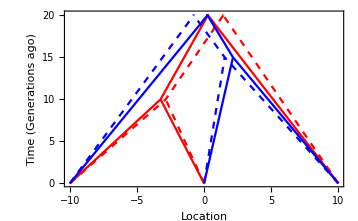

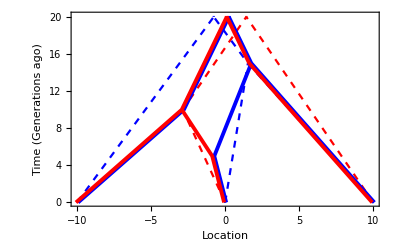

```mathematica
IndependentTree1 =ListLinePlot[{{{l1,0},{loc1[[1]][[1]],t-t1},{μ1[[1]][[1]],t}},{{l2,0}, {loc1[[1]][[1]],t-t1} }, {{l3,0},{μ1[[1]][[1]],t}},{{μ1[[1]][[1]],t}, {μ1[[1]][[1]],t+te}} }/.Params,PlotStyle->{{Red,Dashed}} , PlotLegends-> Placed[LineLegend[{"Tree 1 (Comp)"},LegendMarkerSize->20],{Right, Top}]];
CompTree1 =ListLinePlot[{{{l1,0},{l1Comp[[1]][[1]],t-t1},{le1Comp[[1]][[1]],t},{μComp[[1]][[1]],t+te}},{{l2,0}, {l1Comp[[1]][[1]],t-t1} }, {{l3,0},{le1Comp[[1]][[1]],t}},{{le1Comp[[1]][[1]],t}, {μComp[[1]][[1]],t+te}} }/.Params,PlotStyle->{{Red}} , PlotLegends-> Placed[LineLegend[{"Tree 1 (ARG)"},LegendMarkerSize->20],{Right,Top}]];
ARGTree1 =ListLinePlot[{{{l1-dev,0},{l1ARG[[1]][[1]]-dev,t-t1},{μARG[[1]][[1]]-dev,t},{μARG[[1]][[1]]-dev,t+te}},{{l2-dev,0}, {l3ARG[[1]][[1]]-dev,t3},{l1ARG[[1]][[1]]-dev,t-t1} }, {{l3-dev,0},{l2ARG[[1]][[1]]-dev,t-t2},{μARG[[1]][[1]]-dev,t}} }/.Params,PlotStyle->Directive[Red, Thickness[0.007]] , PlotLegends-> Placed[LineLegend[{"Tree 1 (ARG)"},LegendMarkerSize->20],{Right,Top}]];

IndependentTree2 =ListLinePlot[{{{l3,0},{loc2[[1]][[1]],t-t2},{μ2[[1]][[1]],t}},{{l2,0}, {loc2[[1]][[1]],t-t2} }, {{l1,0},{μ2[[1]][[1]],t}},{{μ2[[1]][[1]],t} ,{μ2[[1]][[1]],t+te}} }/.Params,PlotStyle->{{Blue,Dashed}}  , PlotLegends-> Placed[LineLegend[{"Tree 2 (Comp)"},LegendMarkerSize->20],{Left,Top}]];
CompTree2 =ListLinePlot[{{{l3,0},{l2Comp[[1]][[1]],t-t2},{le2Comp[[1]][[1]],t},{μComp[[1]][[1]],t+te}},{{l2,0}, {l2Comp[[1]][[1]],t-t2} }, {{l1,0},{le2Comp[[1]][[1]],t}},{{le2Comp[[1]][[1]],t}, {μComp[[1]][[1]],t+te}} }/.Params,PlotStyle->{{Blue}} , PlotLegends-> Placed[LineLegend[{"Tree 2 (ARG)"},LegendMarkerSize->20],{Left,Top}]];
ARGTree2 =ListLinePlot[{{{l1+dev,0},{l1ARG[[1]][[1]]+dev,t-t1},{μARG[[1]][[1]]+dev,t},{μARG[[1]][[1]]+dev,t+te}},{{l2+dev,0}, {l3ARG[[1]][[1]]+dev,t3},{l2ARG[[1]][[1]]+dev,t-t2} }, {{l3+dev,0},{l2ARG[[1]][[1]]+dev,t-t2},{μARG[[1]][[1]]+dev,t}} }/.Params,PlotStyle->Directive[Blue,Thickness[0.007]] , PlotLegends-> Placed[LineLegend[{"Tree 1 (ARG)"},LegendMarkerSize->20],{Left,Top}]];

Show[IndependentTree1,IndependentTree2,CompTree1,CompTree2, Frame->True, Axes -> {False,False},FrameStyle-> Directive[Black,15],FrameLabel->{"Location","Time (Generations ago)"}]
Show[IndependentTree1,IndependentTree2,ARGTree2,ARGTree1, Frame->True, Axes -> {False,False},FrameStyle-> Directive[Black,15],FrameLabel->{"Location","Time (Generations ago)"}]
```

```mathematica
Sqrt[1/Total[Inverse[S1],2]]/.Params
Sqrt[1/Total[Inverse[S2],2]]/.Params
Sqrt[1/Total[Inverse[SARG],2]]/.Params
```

3.70626

3.5996

3.52887

```mathematica
Clear["Global`*"]
Ones[n_] := ConstantArray[1,{n,1}];
Zeros[n_] := ConstantArray[0,{n,1}];

S1 = {{t,t-tx,ty},{t-tx,t,ty},{ty,ty,t}} + te ConstantArray[1,{3,3}] ;
S2 = {{t,t-tx,0},{t-tx,t,0},{0,0,t}} + te ConstantArray[1,{3,3}]; 
SComp = ArrayFlatten[{ {S1, ConstantArray[0,{3,3}]},{ConstantArray[0,{3,3}],S2}}] + te ConstantArray[1,{6,6}];
SComp//MatrixForm
SARG = {{t,t-tz,t-tx,0},{t-tz,t,t-tx-tz,ty},{t-tx,t-tx-tz,t,0},{0,ty,0,t}}+ te ConstantArray[1,{4,4}];
SARG//MatrixForm

l = {{l1},{l2},{l3}};
μ1 = Inverse[Transpose[Ones[3]].Inverse[S1].Ones[3]].Transpose[Ones[3]].Inverse[S1].l//Simplify;
σ1 = Transpose[l - μ1[[1]][[1]] Ones[3]].Inverse[S1].(l - μ1[[1]][[1]] Ones[3])//Simplify;
s1 = {{t-tx},{t-tx},{ty}};
loc1 = μ1 + Transpose[s1].Inverse[S1].(l - μ1[[1]][[1]] Ones[3]);

μ2 = Inverse[Transpose[Ones[3]].Inverse[S2].Ones[3]].Transpose[Ones[3]].Inverse[S2].l//Simplify;
σ2 = Transpose[l - μ2[[1]][[1]] Ones[3]].Inverse[S2].(l - μ2[[1]][[1]] Ones[3])//Simplify;
s2 = {{t-tx},{t-tx},{0}}+ te Ones[3];
loc2 = μ2 + Transpose[s2].Inverse[S2].(l - μ2[[1]][[1]] Ones[3]);

lComp = ArrayFlatten[{{l},{l}}];μComp = Inverse[Transpose[Ones[6]].Inverse[SComp].Ones[6]].Transpose[Ones[6]].Inverse[SComp].lComp//Simplify;
σComp = Transpose[lComp - μComp[[1]][[1]] Ones[6]].Inverse[SComp].(lComp - μComp[[1]][[1]] Ones[6])//Simplify;
s1Comp = ArrayFlatten[{{s1},{Zeros[3]}}]+ te Ones[6];
l1Comp = μComp + Transpose[s1Comp].Inverse[SComp].(lComp - μComp[[1]][[1]] Ones[6]);
s2Comp = ArrayFlatten[{{Zeros[3]},{s2}}] + te Ones[6];
l2Comp = μComp + Transpose[s2Comp].Inverse[SComp].(lComp - μComp[[1]][[1]] Ones[6]);
se1Comp = ArrayFlatten[{{te Ones[3]},{Zeros[3]}}];
le1Comp = μComp + Transpose[se1Comp].Inverse[SComp].(lComp - μComp[[1]][[1]] Ones[6]);
se2Comp = ArrayFlatten[{{Zeros[3]},{te Ones[3]}}] ;
le2Comp = μComp + Transpose[se2Comp].Inverse[SComp].(lComp - μComp[[1]][[1]] Ones[6]);

P = {{1,0,0},{0,1,0},{0,1,0},{0,0,1}};
lARG = P.l;
lARG//MatrixForm
μARG = Inverse[Transpose[Ones[4]].Inverse[SARG].Ones[4]].Transpose[Ones[4]].Inverse[SARG].lARG//Simplify;
σARG = Transpose[lARG - μARG[[1]][[1]] Ones[4]].Inverse[SARG].(lARG - μARG[[1]][[1]] Ones[4])//Simplify;
s1ARG = {{t-tx},{t-tx-tz},{t-tx},{0}} + te Ones[4] ;
l1ARG = μARG + Transpose[s1ARG].Inverse[SARG].(lARG - μARG[[1]][[1]] Ones[4]);
s2ARG = {{tz},{0},{tz},{0}} + te Ones[4];
l2ARG = μARG + Transpose[s2ARG].Inverse[SARG].(lARG - μARG[[1]][[1]] Ones[4]);
s3ARG = {{0},{ty},{0},{ty}} + te Ones[4];
l3ARG = μARG + Transpose[s3ARG].Inverse[SARG].(lARG - μARG[[1]][[1]] Ones[4]);

Params = {t->4,tx->1,ty->1,tz->2,l1->-10,l2->0,l3->10, te -> 0.10000}

N[{σ1[[1]][[1]], σ2[[1]][[1]],(σ1[[1]][[1]]+ σ2[[1]][[1]]), σComp[[1]][[1]], σARG[[1]][[1]]}/.Params]
N[{μ1[[1]][[1]], μ2[[1]][[1]], μComp[[1]][[1]], μARG[[1]][[1]]}/.Params]
l3ARG/.Params//Simplify
```

(t+2 te | t+2 te-tx | 2 te+ty | te | te | te
t+2 te-tx | t+2 te | 2 te+ty | te | te | te
2 te+ty | 2 te+ty | t+2 te | te | te | te
te | te | te | t+2 te | t+2 te-tx | 2 te
te | te | te | t+2 te-tx | t+2 te | 2 te
te | te | te | 2 te | 2 te | t+2 te)

```mathematica
({{t+te, t+te-tz, t+te-tx, te}, {t+te-tz, t+te, t+te-tx-tz, te+ty}, {t+te-tx, t+te-tx-tz, t+te, te}, {te, te+ty, te, t+te}})ss
```

(l1
l2
l2
l3)

{t→4,tx→1,ty→1,tz→2,l1→-10,l2→0,l3→10,te→0.1}

{90.9091,80.,170.909,170.917,85.7143}

{1.81818,2.,1.91929,2.85714}

{{5.71429}}

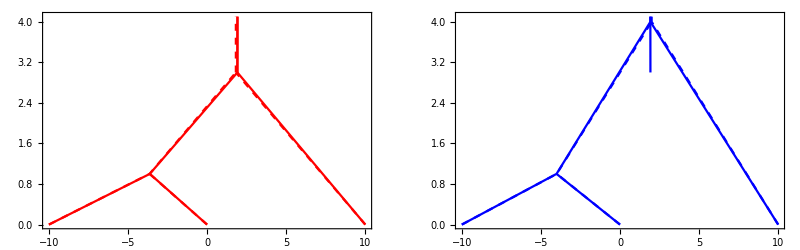

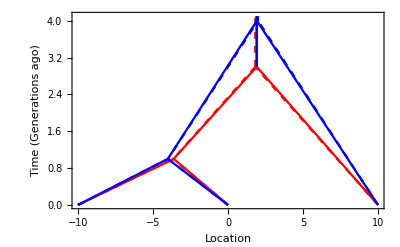

```mathematica
IndependentTree1 =ListLinePlot[{{{l1,0},{loc1[[1]][[1]],tx},{μ1[[1]][[1]],t-ty}},{{l2,0}, {loc1[[1]][[1]],tx} }, {{l3,0},{μ1[[1]][[1]],t-ty}},{{μ1[[1]][[1]],t-ty}, {μ1[[1]][[1]],t+te}} }/.Params,PlotStyle->{{Red,Dashed}} , PlotLegends-> Placed[LineLegend[{"Tree 1 (Comp)"},LegendMarkerSize->20],{Right, Top}]];
CompTree1 =ListLinePlot[{{{l1,0},{l1Comp[[1]][[1]],tx},{le1Comp[[1]][[1]],t-ty},{μComp[[1]][[1]],t+te}},{{l2,0}, {l1Comp[[1]][[1]],tx} }, {{l3,0},{le1Comp[[1]][[1]],t-ty}},{{le1Comp[[1]][[1]],t-ty}, {μComp[[1]][[1]],t+te}} }/.Params,PlotStyle->{{Red}} , PlotLegends-> Placed[LineLegend[{"Tree 1 (ARG)"},LegendMarkerSize->20],{Right,Top}]];


IndependentTree2 =ListLinePlot[{{{l1,0},{loc2[[1]][[1]],tx},{μ2[[1]][[1]],t}},{{l2,0}, {loc2[[1]][[1]],tx} }, {{l3,0},{μ2[[1]][[1]],t}},{{μ2[[1]][[1]],t}, {μ2[[1]][[1]],t+te}} }/.Params,PlotStyle->{{Blue,Dashed}} , PlotLegends-> Placed[LineLegend[{"Tree 1 (Comp)"},LegendMarkerSize->20],{Right, Top}]];
CompTree2 =ListLinePlot[{{{l1,0},{l2Comp[[1]][[1]],tx},{le2Comp[[1]][[1]],t},{μComp[[1]][[1]],t+te}},{{l2,0}, {l2Comp[[1]][[1]],tx} }, {{l3,0},{le2Comp[[1]][[1]],t}},{{le2Comp[[1]][[1]],t-ty}, {μComp[[1]][[1]],t+te}} }/.Params,PlotStyle->{{Blue}} , PlotLegends-> Placed[LineLegend[{"Tree 1 (ARG)"},LegendMarkerSize->20],{Right,Top}]];
GraphicsRow[{Show[IndependentTree1,CompTree1, Frame-> True, Axes ->{False,False}], Show[IndependentTree2,CompTree2, Frame-> True, Axes ->{False,False}]}]

Show[IndependentTree1,IndependentTree2,CompTree1,CompTree2, Frame->True, Axes -> {False,False},FrameStyle-> Directive[Black,15],FrameLabel->{"Location","Time (Generations ago)"}]
```